# Enter title here

## Enter subtitle here

Enter subsubtitle here

## Data Loading & Cleaning

### Data Loading

```mathematica
ds = Import["https://raw.githubusercontent.com/scalabrindario/predicting-climate-risks/main/data/dataset_sample.csv", "Dataset", "HeaderLines" -> 1];(*Import dataset sample*)
comp = Import["https://raw.githubusercontent.com/scalabrindario/predicting-climate-risks/main/data/company_information.csv", "Dataset", "HeaderLines" -> 1];(*Import company information*)
```

### Data Cleaning

```mathematica
ds = KeyDrop[{""}]@ds; (*Drop emtpy column*)
ds = KeyDrop[{"Activity Description"}]@ds; (*Drop activity column*)
ds = ds[All,KeyMap[Replace[{"Ultimate Parent Name"->"Company", "Ultimate Parent ISIN"->"ISIN","ExposureScore_Composite_ModerateHigh_2020" -> "Risk2020",
"ExposureScore_Composite_ModerateHigh_2030" -> "Risk2030","ExposureScore_Composite_ModerateHigh_2040" -> "Risk2040","ExposureScore_Composite_ModerateHigh_2050" -> "Risk2050","ExposureScore_Composite_ModerateHigh_2060" ->"Risk2060",
"ExposureScore_Composite_ModerateHigh_2070" -> "Risk2070","ExposureScore_Composite_ModerateHigh_2080" -> "Risk2080",
"ExposureScore_Composite_ModerateHigh_2090"-> "Risk2090"}]]];(*Rename columns name*)
RandomSample[ds, 5]
comp = KeyDrop[{""}]@comp; (*Drop emtpy column*)
RandomSample[comp, 5]
```

## Feature Engineering

### Integral Score

Our goal it to give a summary of the risk approximation by decade into one scalar statistic, called Integral Score. 
We first visualise several options for this score, given the risk values by decade.
One can fit a function given the risk approximation for several years, and then integrate the resulting curve.
The choice of score then boils down to the choice of approximation.

{62,64,67,68,71,69,73,73}

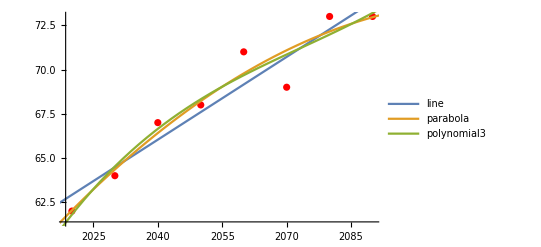

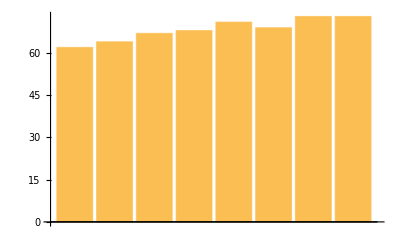

Linear approximation (line): 5532.38

Quardatic approximation (parabola): 5529.05

Third degree approximation (polynomial3): 5535.41

Rectangle approximation (barchart): 5470

```mathematica
x = {2020, 2030, 2040,2050,2060,2070, 2080, 2090};
yRandom = Normal@Values@RandomSample[ds[All, {6;;13}],1][[1,1]] (*We pick one row at random to illustrate all the possible scores*)
data = Transpose@Normal@{x,yRandom};
line = Fit[data, {1,z}, z];
parabola = Fit[data, {1,z,z^2}, z];
polynomial3 = Fit[data, {1,z,z^2,z^3}, z];
Show[ListPlot[data,PlotStyle->Red],Plot[{line, parabola, polynomial3},{z,2010,2100}, PlotLegends->"Expressions"]]
BarChart[yRandom]
Print["Linear approximation (line): ", Integrate[line,{z,2020,2100}]]
Print["Quardatic approximation (parabola): ",Integrate[parabola,{z,2020,2100}]]
Print["Third degree approximation (polynomial3): ",Integrate[polynomial3,{z,2020,2100}]]
Print["Rectangle approximation (barchart): ",(Total@yRandom)*10]
```

We note that all the approximations are in the same order of magnitude. For the sake of simplicity and to avoid overfitting, we choose the linear approximation. We add the chosen Integral Score to the dataset.

```mathematica
intColumn =ds[All,<|"integralScore"->Integrate[
Fit[Transpose@Normal@{x,{#Risk2020,#Risk2030,#Risk2040,#Risk2050,#Risk2060,#Risk2070,#Risk2080,#Risk2090}}, {1,z}, z]
,{z,2020,2100}]|>&];
newds=Join[ds,intColumn,2];
RandomSample[newds, 5]
```

### Computing Average

```mathematica
avgds= newds[GroupBy[{#Company}&]/*Values,<|"Company"->Query[First,"Company"],"ISIN"->Query[First,"ISIN"],"elevation"->Query[Mean,"elevation"],"integralScore"->Query[Mean,"integralScore"]|>] ;(*Grouped and computed operations on some columns*)
newElev = N[Normal[avgds[All, "elevation"]]]; (*Convert to float the numerical values of elevation column*)
ElevDat=Dataset[<|"Elevation"->#|>&/@Normal[newElev]];(*Convert the list into a dataset*)
avgds = Join[avgds,ElevDat,2]; (*Add New elevation column to the dataset*)
avgds = KeyDrop[{"elevation"}]@avgds;
RandomSample[avgds, 5]
```

### Merge the two datasets

```mathematica
merged = JoinAcross[avgds,comp,Key["ISIN"]];(*Merged two datasets and dropped rows without ISIN value*)
RandomSample[merged,5]
```

### Create Ratings

```mathematica
MinMaxScaler[value_]:=Rescale[value,{Min[merged[All, "integralScore"]],Max[merged[All, "integralScore"]]}];
MinMaxScaledList = Map[MinMaxScaler, merged[All, "integralScore"]];
RatingCreator[value_]:= 
If[Between[value,{0,0.2}], "A", 
If[Between[value,{0.2,0.4}], "B", 
If[Between[value,{0.4,0.6}], "C",
If[Between[value,{0.6,0.8}], "D",
If[Between[value,{0.8,1}], "E",   
]]]]]; (*Convert a numerical variable into a category*)
RatingsList = Map[RatingCreator, MinMaxScaledList];
IntScaledDat=Dataset[<|"IntScaled"->#|>&/@Normal[MinMaxScaledList]]; (*Convert the list into a dataset*)
RatingsDat=Dataset[<|"Ratings"->#|>&/@Normal[RatingsList]];(*Convert the list into a dataset*)
finalds = Join[merged,IntScaledDat,2]; (*Add Scaled Integral column to the dataset*)
finalds = Join[finalds,RatingsDat,2];(*Add Rating column to the dataset*)
RandomSample[finalds, 5]
```

## Machine Learning

### Dataset Preparation

```mathematica
datasetML = KeyDrop[{"Company", "ISIN", "TCUID", "integralScore", "IntScaled","Carbon-Scope 1  (tonnes CO2e)", "Carbon-Scope 2  (tonnes CO2e)", "Carbon-Scope 3 (tonnes CO2e)"}]@finalds; (*Drop columns that are not needed for machine learning techniques*)
{nobs,ncol}=Dimensions[datasetML];
{trainingset,testset}=TakeDrop[RandomSample[datasetML],Round[nobs*0.8,1]];
```

### Classification

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"NearestNeighbors"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 7)
Classes | ,,ABCDE
Accuracy | (33.8.) %
Method | NearestNeighbors
Single evaluation time | 2.33 ms/example
Batch evaluation speed | 38.1 examples/ms
Loss | 1.58 ± 0.12
Model memory | 289. kB
Training examples used | 75 examples
Training time | 166. ms
 |

0.368421

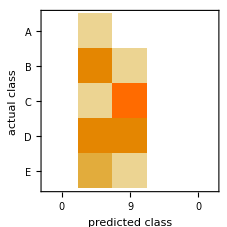

```mathematica
cm =ClassifierMeasurements[cRisk,testset];
cm["Accuracy"]
cm["ConfusionMatrixPlot"]
```

### Clustering

{59.7857,140.378,130.778,5.,144.245,663.,10.,104.056,196.625,28.6,116.667,5.,53.3333,39.5,136.857,86.,38.,365.5,11.,28.3333,151.821,12.,106.286,193.1,89.125,47.,10.,50.,254.,28.2,619.,25.6667,49.3333,21.,4.,36.6667,9.,39.,158.,7.5,171.25,66.3333,36.8,1094.17,8.125,7.45455,50.,7.,10.,59.,12.,24.,13.,38.,34.,12.,36.,184.,55.,290.5,1075.5,14.,6.,16.,3.,15.,20.3333,52.,9.5,259.667,14.,4.,6.,9.33333,88.,65.3333,498.667,1110.,11.,16.,48.3333,69.6667,2.,15.,55.,144.,482.,4.,5.,4.,494.,4.,20.,790.}

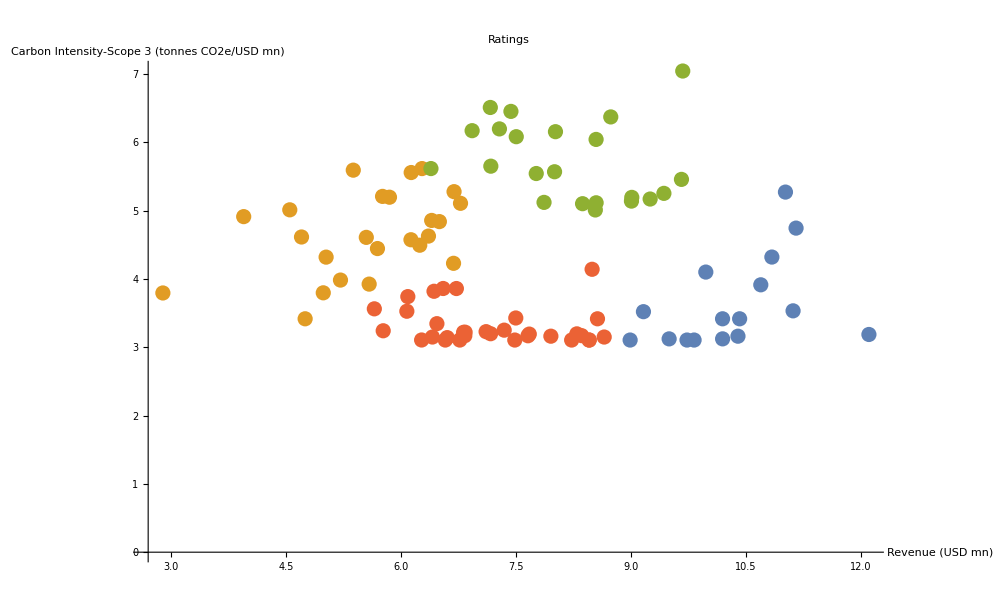

```mathematica
data = Log@Transpose @Normal@{datasetML[All,"Revenue (USD mn)"],datasetML[All,"Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"]};
ListPlot[FindClusters[data],PlotLabel -> "Ratings",AxesLabel -> {"Revenue (USD mn)","Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"}]
```

```mathematica
Normal[Keys[datasetML]]
```

{{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings},{elevation,GICS Sector Name,Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),Ratings}}